### Start choosing the example:

```mathematica
t=4;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.010511,Null}

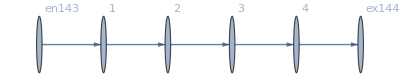

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j145→80.,j146→80.,j147→80.,j148→80.,j149→80.,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80.,jt157→80.,jt158→0.,jt159→80.,jt160→0.,jt161→80.,jt162→0.,u163→255.,u164→175.,u165→95.,u166→15.,u167→255.,u168→175.,u169→95.,u170→15.,u171→15.,u172→255.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→22.7459,u164→20.1639,u165→17.582,u166→15.,u167→22.7459,u168→20.1639,u169→17.582,u170→15.,u171→15.,u172→22.7459|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→24.484,u164→21.3227,u165→18.1613,u166→15.,u167→24.484,u168→21.3227,u169→18.1613,u170→15.,u171→15.,u172→24.484|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→30.0717,u164→25.0478,u165→20.0239,u166→15.,u167→30.0717,u168→25.0478,u169→20.0239,u170→15.,u171→15.,u172→30.0717|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.47684×10^-13,ComplexInfinity]

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→255.,u164→175.,u165→95.,u166→15.,u167→255.,u168→175.,u169→95.,u170→15.,u171→15.,u172→255.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→1106.72,u164→742.811,u165→378.906,u166→15.,u167→1106.72,u168→742.811,u169→378.906,u170→15.,u171→15.,u172→1106.72|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→870144.,u164→580101.,u165→290058.,u166→15.,u167→870144.,u168→580101.,u169→290058.,u170→15.,u171→15.,u172→870144.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.37917×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.37917×10^-16

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→4.6785×10^7,u164→3.119×10^7,u165→1.5595×10^7,u166→15.,u167→4.6785×10^7,u168→3.119×10^7,u169→1.5595×10^7,u170→15.,u171→15.,u172→4.6785×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.83133×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.83133×10^-16

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→7.21578×10^10,u164→4.81052×10^10,u165→2.40526×10^10,u166→15.,u167→7.21578×10^10,u168→4.81052×10^10,u169→2.40526×10^10,u170→15.,u171→15.,u172→7.21578×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→1.68111×10^19,u164→1.12074×10^19,u165→5.6037×10^18,u166→15.,u167→1.68111×10^19,u168→1.12074×10^19,u169→5.6037×10^18,u170→15.,u171→15.,u172→1.68111×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

<|j145→80,j146→80,j147→80,j148→80,j149→80,j150→0.,j151→0.,j152→0.,j153→0.,j154→0.,jt155→0.,jt156→80,jt157→80,jt158→0.,jt159→80,jt160→0.,jt161→80,jt162→0.,u163→6.61469×10^106,u164→4.4098×10^106,u165→2.2049×10^106,u166→15.,u167→6.61469×10^106,u168→4.4098×10^106,u169→2.2049×10^106,u170→15.,u171→15.,u172→6.61469×10^106|>